```mathematica
Quit[]
```

```mathematica
<<BBHpnToolkit`
```

Authors: Rickmoy Samanta(rickmoysamanta@gmail.com); Sashwat Tanay (sashwattanay@gmail.com, https://sashwattanay.github.io/sashwat_site/)

```mathematica
(*User input*)
m1=5/2  ;            (*bigger mass*)
m2=1    ;              (*smaller mass*)
tf=1000. ; 
ϵ=1./1000           (* This is 1/c^2 *);
R=2{ 1,1,1};
P=1{1/2,-1/2,1/3};
S1={0,1,1}√ϵ  ;              S2={1,-3/10,0}√ϵ;   

(*S1 and S2 (with √ϵ included) are the spin angular momenta of the two black holes. Their dimension is same as that of orbital angular momentum L = R x P. *)
```

# Frequencies

```mathematica
freqArr= frequency[m1,m2,R,P,S1,S2,ϵ][[2]]             (*The 5 frequencies (within the action-angle framework) of the system*)
```

{0.000102314,0.,0.214619,0.214141,0.000127328}

# BBH system at a later time

```mathematica
(*State of the system at time = tf. We are giving {R,P,S1,S2}*)        

NmHflow[m1,m2,R,P,S1,S2,tf  ,ϵ]                   (*got via numerical integration of Hamilton's equations*)  
Acflow[m1,m2,R,P,S1,S2,tf  ,ϵ]                     (*got from the closed-form solution via integrating the Hamilton's equations as in arXiv:1908.02927 (with 1PN effects added)*)
Hflow[m1,m2,R,P,S1,S2,tf  ,ϵ]                       (*got from the action-angle-based closed-form solution as given in arXiv:2110.15351 and arXiv:2012.06586 *)
```

{{2.8575,-2.21954,2.00275},{-0.0808955,-0.636844,-0.175961},{0.00285825,0.0293504,0.0336212},{0.0294534,-0.0146733,-0.00268159}}

{{2.86621,-2.21029,2.01161},{-0.0789682,-0.636646,-0.174325},{0.00285842,0.0293506,0.033621},{0.0294388,-0.0146787,-0.0026943}}

{{2.86621,-2.21029,2.01161},{-0.0789682,-0.636646,-0.174325},{0.00285842,0.0293506,0.033621},{0.0294388,-0.0146787,-0.0026943}}

# error computation

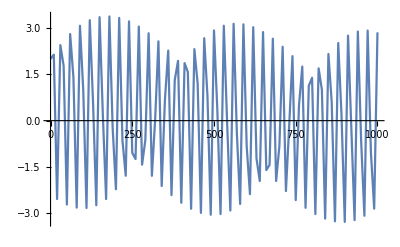

```mathematica
ϵ=1./1000 ;ListLinePlot[Table[{t,NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]][[1]]},{t,0,1000,10}]]
```

```mathematica
Clear[ϵ]
data=Table[{ϵ, 1/Norm[NmHflow[m1,m2,R,P,S1,S2,tf  ,ϵ][[1]]] Abs[Norm[NmHflow[m1,m2,R,P,S1,S2,tf  ,ϵ][[1]]]-Norm[Acflow[m1,m2,R,P,S1,S2,tf  ,ϵ][[1]]]]},{ϵ,1./1000  ,1./100,1./1000  }]
```

{{0.001,0.00129835},{0.002,0.00135845},{0.003,0.000451345},{0.004,0.00247657},{0.005,0.00935247},{0.006,0.0208206},{0.007,0.00413027},{0.008,0.0420018},{0.009,0.0379762},{0.01,0.0209356}}

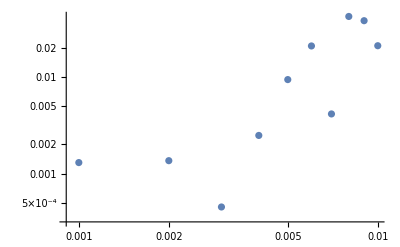

```mathematica
ListLogLogPlot[data]
```